Άσκηση 4

Να γίνει το φάσμα ισχύος για το εκκρεμές (ω_0=1), για θ(0)=3.14. Να βελτιωθεί ώστε να γίνει όσο πιο καθαρό γίνεται.

Λύση

Ορίζουμε το δυναμικό και υπολογίζουμε την ενέργεια.

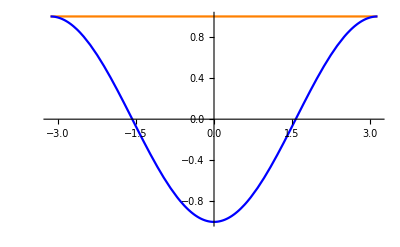

```mathematica
ClearAll["Global`*"]
U[θ_]:=-Cos[θ];
E0=U[3.14];
Plot[{E0,U[θ]},{θ,-π,π},PlotStyle->{Orange,Blue}]
```

Υπολογίζουμε την περίοδο της ταλάντωσης, για να την χρησιμοποιήσουμε στην ολοκλήρωση.

```mathematica
Tperiod=2 NIntegrate[1/(√(2(E0-U[θ]))),{θ,-3.14,3.14}]
```

34.0872

Λύνουμε την διαφορική εξίσωση της κίνησης.

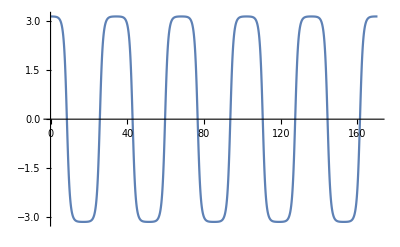

```mathematica
deq=θ''[t]==-Sin[θ[t]];
tmax=5Tperiod;
th[t_]=θ[t]/.(NDSolve[{deq,θ[0]==3.14,θ'[0]==0},θ,{t,0,tmax}]//Flatten);
Plot[th[t],{t,0,tmax}]
```

Παίρνουμε τιμές για να φτιάξουμε το δείγμα μας.

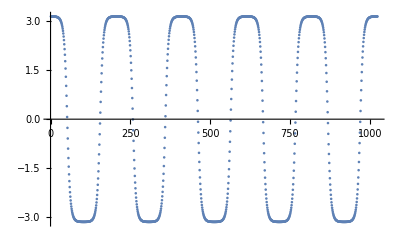

```mathematica
ndata=2^10;
dt=tmax/ndata;
sample=Table[th[i dt],{i,0,ndata-1}];
ListPlot[sample]
```

Χρησιμοποιούμε τον διακριτό μετασχηματισμό Fourier.

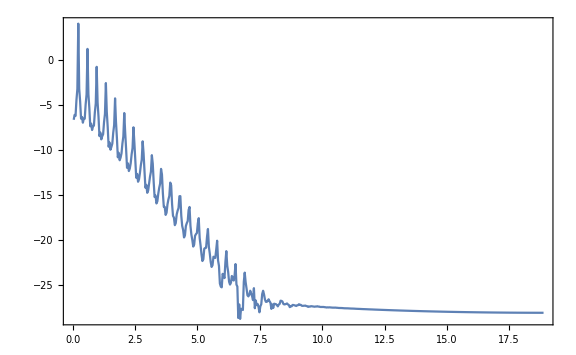

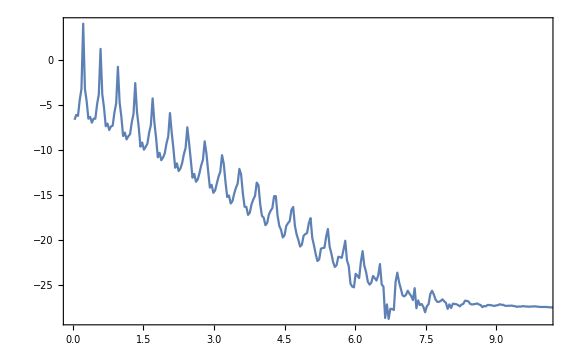

```mathematica
fdata=Fourier[sample];
powerSpectrum=Table[{i 2Pi/tmax,Log[(Re[fdata[[i]]]^2+Im[fdata[[i]]]^2)/(2 √ndata)]},{i,1,ndata/2}];
lp=ListPlot[powerSpectrum,Joined->True,PlotRange->All,Frame->True,ImageSize->Large]
Show[lp,PlotRange->{{0,10},All}]
```